## In Class Challenges - W3C2

### Cameron Embree - Armageddon group

Challenge 1: -Graphics-

```mathematica
(*Challenge 1 solution by:*)
```

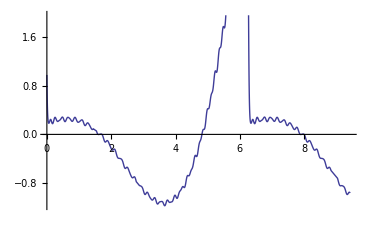

{6.07758,{x→-0.061245}}

-((E^((-I)*x))^x*LerchPhi[E^((-I)*x), 1, 1 + x] + 
   E^((2*I)*x)*(E^(I*x))^x*LerchPhi[E^(I*x), 1, 1 + x] + 
   E^(I*x)*Log[1 - E^(I*x)] + E^(I*x)*Log[(-1 + E^(I*x))/E^(I*x)])/
 (2*E^(I*x))

```mathematica
f[x_]:=Sin[x]-E^(-∑_(k=1)^30 Cos[k*x]/k)+E^(-∑_(k=1)^50 Sin[k*x]/k)
Plot[f[x],{x,0,3*π}]
NMaximize[f[x],x]
```

Challenge 2: -Graphics-

```mathematica
(*Challenge 2 solution by:*)
```

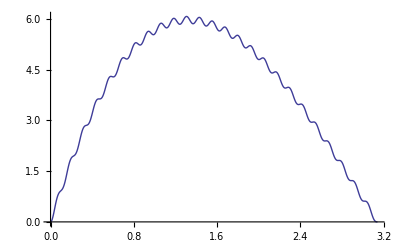

```mathematica
func2[x_]:=x(2*π-x)*∑_(n=1)^50 Sin[n*x]/n
Plot[func2[x],{x,0,π}]
```

Challenge 3: Plot the graphs of the functions 2 exp(−x^2) and cos(sin(x) + cos(x)) be- tween [−π, π] on the same graph.

```mathematica
(*Challenge 3 solution by:*)
```

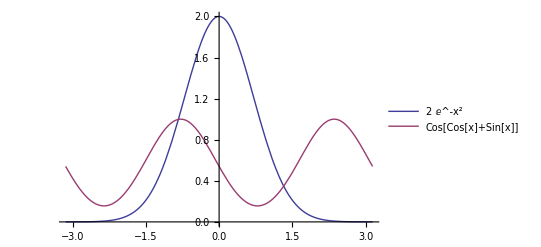

```mathematica
func31[x_]:=2 *Exp[−x^2]
func32[x_]:=Cos[Sin[x]+Cos[x]]
Plot[{func31[x], func32[x]},{x,-π,π}, PlotLegends->{func31[x],func32[x]}]
```

Challenge 4: Plot the graph of the inequality | x^2 + y |≤| y^2 + x | .

```mathematica
(*Challenge 4 solution by:*)
```

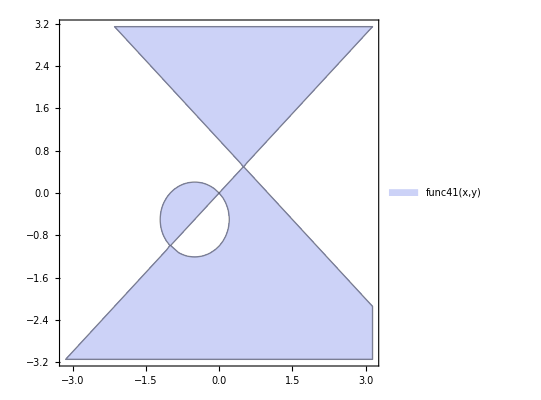

```mathematica
func41[x_,y_]:=Abs[x^2+y]≤Abs[y^2+x]
RegionPlot[func41[x,y],{x,-π,π},{y,-π,π}, PlotLegends->"Expressions"]
```

Challenge 5: Define the Conway recursive sequence a(1) = 1, a(2) = 1 and a(n) = a(a(n − 1)) + a(n − a(n − 1))
in Mathematica, and plot a(n)/n when n runs from 1 to 1500.

```mathematica
(*Challenge 5 solution by:*)
```

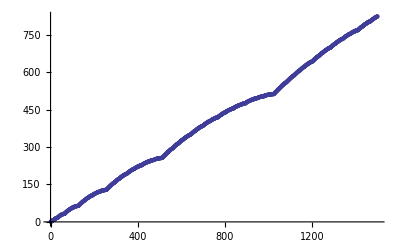

```mathematica
a[x_]:=rl[[rl[[x−1]]]]+rl[[x−rl[[x−1]]]]

rl={1,1};

n=3;While[n<1500,AppendTo[rl,a[n]];n++]

(*
(*Still do not know why the while loop only executes once...*)
Block[{m=3,n=1500},
While[m<n;AppendTo[rl,a[m]];m++];
]
*)

rl;
ListPlot[rl]
```

Challenge 6: Plot the graph of 6x^2−2x^4−y^2z^2 =0.

```mathematica
(*Challenge 6 solution by:*)
```

```mathematica
ContourPlot3D[6x^2−2x^4−y^2z^2,{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-

Challenge 7:  Look at http://reference.wolfram.com/mathematica/guide/ChartingAndInformationVisualization.html, and create some cool charts.

```mathematica
(*Challenge 7 solution by:*)
```

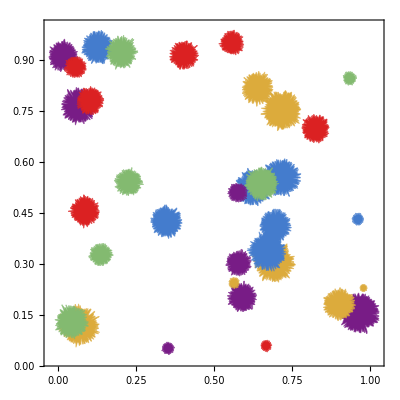

-Graphics3D-

```mathematica
BubbleChart[RandomReal[1,{5,7,3}],ChartStyle->"Rainbow", ChartElementFunction->"NoiseBubble"]

BubbleChart3D[RandomReal[1,{5,10,4}],ChartStyle->"DarkRainbow"]

Manipulate[AngularGauge[n,{0,100}],{n,0,100}]
```

Challenge 8: Using CountryData, make some interest charts or plots.

```mathematica
(*Challenge 8 solution by:*)
```

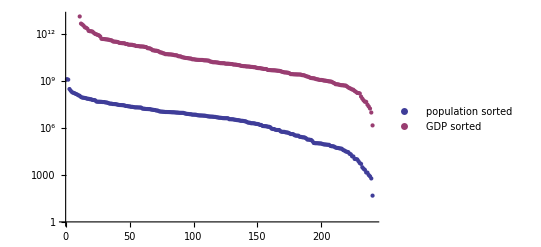

{Canada,France,Germany,Italy,Japan,Russia,UnitedKingdom,UnitedStates}

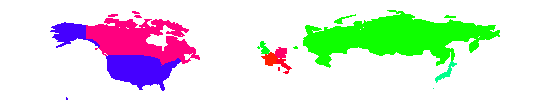

```mathematica
poplist=Reverse[Sort[CountryData[#,"Population"]&/@CountryData[]]];
GDPlist=Reverse[Sort[CountryData[#,"GDP"]&/@CountryData[]]];

ListLogPlot[{poplist,GDPlist}, PlotLegends->{"population sorted", "GDP sorted"}]


CountryData["G8"]
Graphics[{If[MemberQ[allCountries,#],Hue[Random[]]],CountryData[#,"SchematicPolygon"]}&/@CountryData["G8"]]
```

Challenge 9: Using the Graphics fuction, build some polygons and, color them.

```mathematica
(*Challenge 9 solution by:*)
```





```mathematica
Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}},VertexColors->{Red,Green,Blue}]]
Graphics[Polygon[{{1,0},{1,1},{0,1},{0,0}},VertexColors->{Red,Blue}]]
```

Challenge 10: Modify or build upon a “Neat Example” for the CountryData function description(http://reference.wolfram.com/mathematica/ref/CountryData.html).

```mathematica
(*Challenge 10 solution by:*)
```

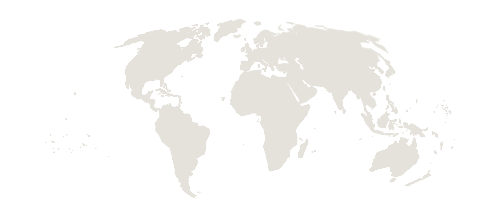

CountryData::notent: "{\"Afghanistan\", \"Albania\", \"Algeria\", \"AmericanSamoa\", \"Andorra\", \"Angola\", \"Anguilla\", \"AntiguaBarbuda\", \"Argentina\", \"Armenia\", \"Aruba\", " … " \"Uzbekistan\", \"Vanuatu\", \"VaticanCity\", \"Venezuela\", \"Vietnam\", \"WallisFutuna\", \"WestBank\", \"WesternSahara\", \"Yemen\", \"Zambia\", \"Zimbabwe\"}" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

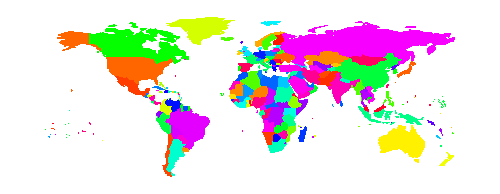

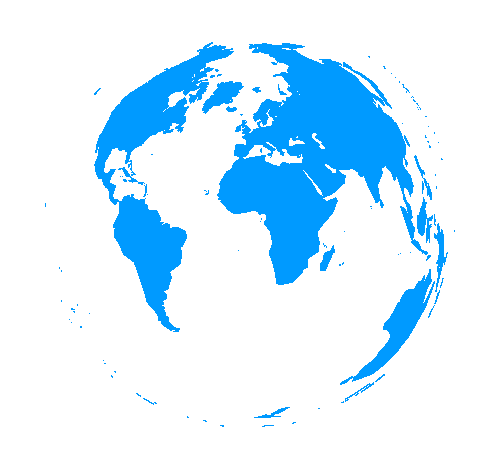

```mathematica
CountryData["World",{"Shape","Mollweide"}]

CountryData[CountryData[All],"Population"];


allCountries=CountryData[All];
Graphics[{If[MemberQ[allCountries,#],Hue[Random[]]],CountryData[#,"SchematicPolygon"]}&/@CountryData[]]

Graphics[{Hue[Random[]],CountryData[#,{"SchematicPolygon","LambertAzimuthal"}]&/@CountryData[]}]

(*CountryData[#,"SchematicPolygon"]&/@CountryData[][[1;;2]]*)
```

Challenge 11: Can you import this PDF on Student Demographics and make cool charts with in? http://www.csuci.edu/ir/student-demographics/spring2013all.pdf

```mathematica
(*Challenge 11 solution by:*)
```

Challenge 12:  You know how to find and import data, do cool things to visualize the data, be creative.